# Laboratory 1 Basics of Mathematica

Henry Osei

Exercise 5. Compute the following.Give approximate values to 10 decimal places when appropriate.
(a) 51!  (b)27! / 25!        (c)log_10 235
(d)ln 71    (e)log_2 1024       (f)sin (π/10)
(g)sin^-1 0.25     (h)√7       (i)cos 1.6
(j)ln e^3           (k)|-2.3|     (l)tan (π/6)

```mathematica
N[51!,10]
```

1.551118753×10^66

```mathematica
N[{27!/25!},10]
```

{702.}

```mathematica
N[Log[10,235],10]
```

2.371067862

```mathematica
Log[71]
```

```mathematica
Log[71]
```

```mathematica
N[Log[2,1024],10]
```

10.

```mathematica
N[Sin[Pi/10],10]
```

0.3090169944

```mathematica
N[ArcSin[0.25],10]
```

0.25268

```mathematica
N[Sqrt[7],10]
```

2.645751311

```mathematica
Cos[1.6]
```

-0.0291995

```mathematica
Log[E^3]
```

3

```mathematica
Abs[-2.3]
```

2.3

```mathematica
N[Tan[Pi/6],10]
```

0.5773502692

Exercise 6. Define the functions f(x)=sin x and g(x)=x^2-3. Then find the following numbers and functions, giving numerical approximations when appropriate.
(a) f(π/6)			(b) g(t)			(c) f( g(2) )	
(d) g( f(x) )			(e) g(g(t))

```mathematica
Clear[f,x]
f[x_]:=Sin[x]
Clear[g,x]
g[x_]=x^2-3
f[Pi/6]
```

-3+x^2

1/2

```mathematica
g[t]
```

-3+t^2

```mathematica
N[f[g[2]]]
```

0.841471

```mathematica
g[f[x]]
```

-3+Sin[x]^2

```mathematica
g[g[t]]
```

-3+(-3+t^2)^2

Exercise 7. 
(a) Plot the graph of the polynomialx^2+3in the interval[-2, 2].			
(b) Define g(t)=tan (t/2) and graph it in the interval [-3, 3].			
(c) Defineh(x) = sin(x^2) and graph it in the interval [-2,3].

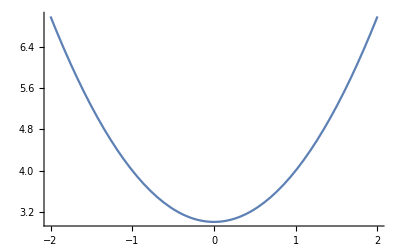

```mathematica
Plot[x^2+3,{x,-2,2}]
```

```mathematica
Clear[g,t]
```

```mathematica
g[t_]:=Tan[t/2]
```

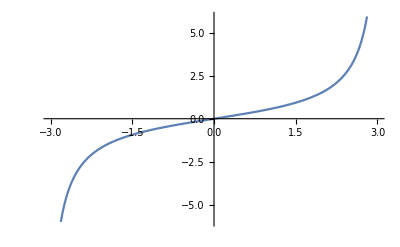

```mathematica
Plot[g[t],{t,-3,3}]
```

```mathematica
Clear [h,x]
```

```mathematica
h[x_]:=Sin[x^2]
```

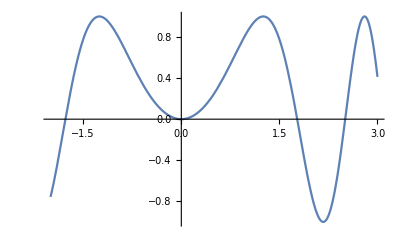

```mathematica
Plot[h[x],{x,-2,3}]
```